# Localiser la foudre

Ce document décrit le principe derrière la localisation de la foudre.  On utilise des antennes dont on connaît la localisation précise :

P_1 = {3.39411,3.39411}

P_2 = {-3.39411,3.39411}

P_3 = {-3.39411,-3.39411}

P_4 = {3.39411,-3.39411}

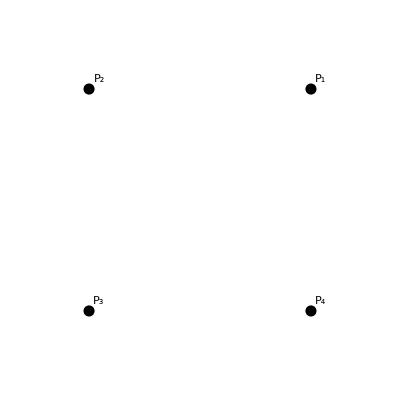

```mathematica
n=4; (* Le nombre d'antennes *)
Table[Subscript[P, i]=4.8{Cos[2π i/n-π/n], Sin[2π i/n-π/n]}, {i, 1, n}];
Table[
Print[Subscript["P", i], " = ", N@Subscript[P, i]],
{i, 1, n}];

(* On affiche les antennes *)
Show[
gPoints=Table[Subscript[gP, i]=
Graphics[{Black, PointSize[.02], Point[Subscript[P, i]],
Text[Subscript["P", i], Offset[{10, 10}, Subscript[P, i]]]}],
{i, 1, n}
],
Axes->False,
PlotRange->{xrange={-5, 5}, yrange={-5, 5}}
]
```

Au temps T (inconnu), un éclair frappe à une position X (inconnue), et crée une onde d’amplitude A (inconnue). Les antennes reçoivent des signaux (ici, on les simule pour le fun... ) et on va utiliser les signaux reçus (temps t_i et amplitudes a_i) pour déterminer d’où ces signaux proviennent.

t_1 = 0.523807

t_2 = 1.68856

t_3 = 2.38548

t_4 = 1.88136

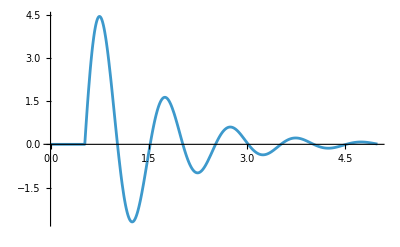
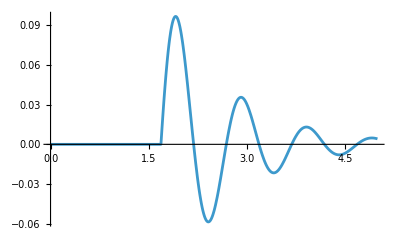
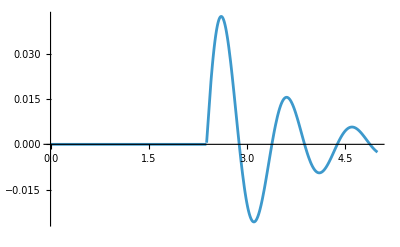
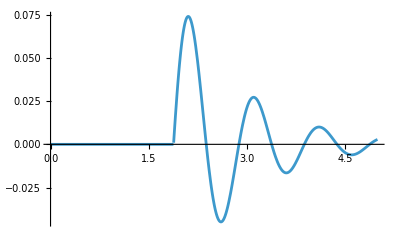
(Signal à P)_1 | -Graphics-
(Signal à P)_2 | -Graphics-
(Signal à P)_3 | -Graphics-
(Signal à P)_4 | -Graphics-

```mathematica
(* Forme de l'onde *)
onde[t_]:=Piecewise[{{Sin[2π t] Exp[- t], t>0}, {0, True}}]

(* Temps, amplitude, position de l'éclair -- toutes inconnues *)
T=RandomReal[{0, 1}];
A=RandomReal[{1, 2}];
X=RandomReal[{-5, 5}, 2];

(* Les distances de l'éclair (inconnues) et les temps où on reçoit les signaux. On assume que les signaux vont à une vitesse de 5 u/s*)
vitesse = 5;
Table[Subscript[d, i]=Norm[X-Subscript[P, i]], {i, 1, n}];
Table[Print[Subscript["t", i], " = ", Subscript[t, i]=T+Subscript[d, i]/vitesse], {i, 1, n}];
Table[Subscript[a, i]=(5 A)/Subscript[d, i]^2, {i, 1, n}];
(* On imprime les signaux reçus par les différentes antennes *)
Grid[Transpose@{
Table[Subscript["Signal à P", i], {i, 1, n}],
plots=Table[
Plot[Subscript[a, i] onde[u-Subscript[t, i]], {u, 0, 5}, PlotRange->{{0, 5}, All}],
{i, 1, n}]
}
]
```

## Triangulation par hyperboles

En regardant les différences de distances entre les temps de parcours, on peut connaître les différences de distances δ_(i, j) de X à deux antennes P_i et P_j; cela nous permet d’établir que le point se situe sur une hyperbole.

δ_(1,2) = 5.82379

δ_(1,3) = 9.30838

δ_(1,4) = 6.78779

δ_(2,3) = 3.48459

δ_(2,4) = 0.964005

δ_(3,4) = 2.52059

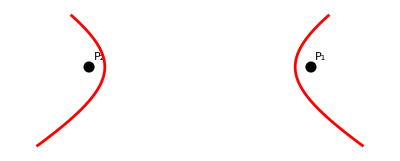

```mathematica
Table[Table[
Print[Subscript["δ", i, j], " = ", 
Subscript[δ, i, j]=Abs[vitesse(Subscript[t, i]-Subscript[t, j])]],
{j, i+1, n}], {i, 1, n}];
r={x, y};
gHyperboles =Table[Table[
Subscript[gH, i, j]=ContourPlot[Subscript[δ, i, j]^2==(Norm[r-Subscript[P, i]]-Norm[r-Subscript[P, j]])^2,{x, -5, 5}, {y, -5, 5}, ContourStyle->Red,PlotPoints->200] ,
{j, i+1, n}], {i, 1, n}];
Show[Subscript[gP, 1], Subscript[gP, 2], Subscript[gH, 1, 2]]
```

En ajoutant plus de points, on peut recouper ces hyperboles pour déterminer où notre point se trouve :

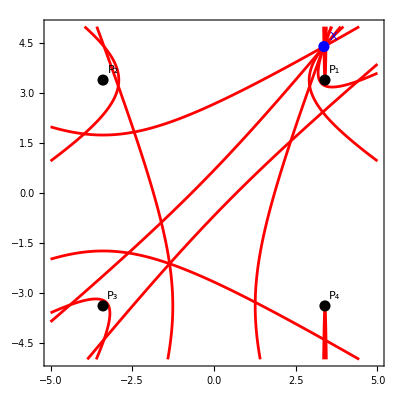

```mathematica
Show[gHyperboles, gPoints, gX=Graphics[{Blue, PointSize[.02], Point[X], Text["X", Offset[{10, 10}, X]]}]]
```